```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/equivalence_classes.m

## Diagrams generation

## Topologies

### ExcludeTopologies filter

Pattern of the topologies which contributes to the form factor in the γμμ vertex:

```mathematica
formFactorPattern=Topology[s_][p1___,Propagator[Incoming][Vertex[1][nIn1_],Vertex[3][nJoin_]],p2___,Propagator[Incoming][Vertex[1][nIn2_],Vertex[3][nJoin_]],p3___];
```

We define the filter for the ExcludeTopologies option in the CreateTopologies function, to study only the muon vertex contributions:

```mathematica
$ExcludeTopologies[MuonVertex]:=MatchQ[#,formFactorPattern]&;
```

```mathematica
excludeTopologies[t_TopologyList]:=Select[t,MatchQ[#,formFactorPattern]&];
excludeTopologies[t_TopologyList]:=Select[t,(MatchQ[#,formFactorPattern]&&Length[Cases[#,Propagator[Internal][_,_],Infinity]]===1)&];
```

### Born

```mathematica
topologiesBornCheck=CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,WFCorrections}];
topologiesBorn=excludeTopologies[topologiesBornCheck];
Print["Number of topologies: ",{topologiesBornCheck,topologiesBorn}//Map[Length]]
```

Number of topologies: {4,1}

#### Unfiltered

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams



Number of topologies: 4

```mathematica
Paint[topologiesBornCheck];
Print["Number of topologies: ",topologiesBornCheck//Length]
```

#### Filtered

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

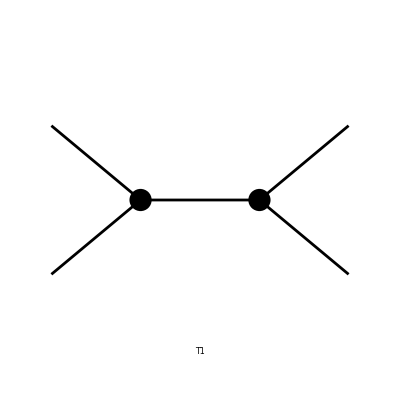

Number of topologies: 1

```mathematica
Paint[topologiesBorn];
Print["Number of topologies: ",topologiesBorn//Length]
```

### 1-Loop

```mathematica
topologies1LCheck=CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,WFCorrections}];
topologies1L=excludeTopologies[topologies1LCheck];
Print["Number of topologies: ",{topologies1LCheck,topologies1L}//Map[Length]]
```

Number of topologies: {42,4}

#### Unfiltered

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 8 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 9 aebf/cfdg/fhegehgh.m, 0 diagrams

> Top. 10 aebf/cgde/ehfgfhgh.m, 0 diagrams

> Top. 11 aebf/cgdf/fhegehgh.m, 0 diagrams

> Top. 12 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 13 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 14 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 15 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 16 aebe/cfdf/efef.m, 0 diagrams

> Top. 17 aebf/cedf/efef.m, 0 diagrams

> Top. 18 aebf/cfde/efef.m, 0 diagrams

> Top. 19 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 20 aebe/cfdg/egfgfg.m, 0 diagrams

> Top. 21 aebe/cfdg/efgfgf.m, 0 diagrams

> Top. 22 aebe/cfdf/eggfgf.m, 0 diagrams

> Top. 23 aebf/cedf/egfggg.m, 0 diagrams

> Top. 24 aebf/cedg/egfgfg.m, 0 diagrams

> Top. 25 aebf/cfde/egfggg.m, 0 diagrams

> Top. 26 aebf/cfdg/fgegeg.m, 0 diagrams

> Top. 27 aebf/cgde/egfgfg.m, 0 diagrams

> Top. 28 aebf/cgdf/fgegeg.m, 0 diagrams

> Top. 29 aebf/cedg/efgfgf.m, 0 diagrams

> Top. 30 aebf/cedf/eggfgf.m, 0 diagrams

> Top. 31 aebf/cgde/efgfgf.m, 0 diagrams

> Top. 32 aebf/cgdg/gfefef.m, 0 diagrams

> Top. 33 aebf/cfde/eggfgf.m, 0 diagrams

> Top. 34 aebf/cfdg/fegege.m, 0 diagrams

> Top. 35 aebf/cfde/fggege.m, 0 diagrams

> Top. 36 aebf/cgdf/fegege.m, 0 diagrams

> Top. 37 aebf/cgdg/gefefe.m, 0 diagrams

> Top. 38 aebf/cedf/fggege.m, 0 diagrams

> Top. 39 aebe/cfdf/fggege.m, 0 diagrams

> Top. 40 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 41 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 42 aebf/cfde/egfhghgh.m, 0 diagrams

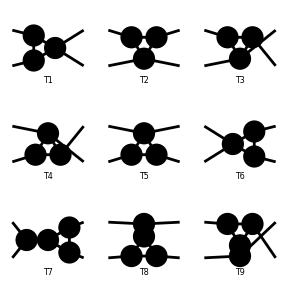

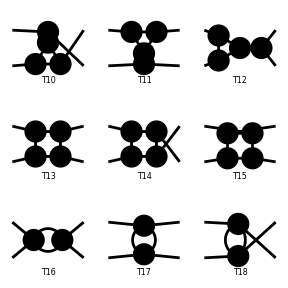

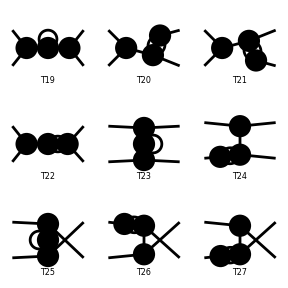

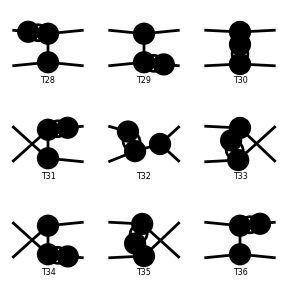

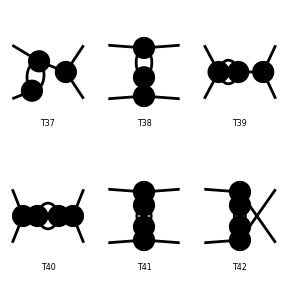

Number of topologies: 42

```mathematica
Paint[topologies1LCheck];
Print["Number of topologies: ",topologies1LCheck//Length]
```

#### Filtered

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebe/cfdg/egfgfg.m, 0 diagrams

> Top. 3 aebe/cfdg/efgfgf.m, 0 diagrams

> Top. 4 aebe/cfdf/eggfgf.m, 0 diagrams

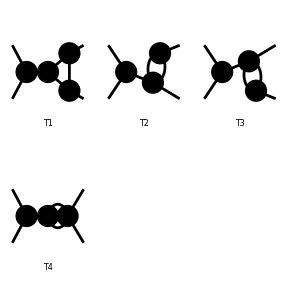

Number of topologies: 4

```mathematica
Paint[topologies1L];
Print["Number of topologies: ",topologies1L//Length]
```

## Insert Fields

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

### Born

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
fieldsBorn=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[10]]&];
Print["Number of diagrams: ",fieldsBorn//Length]
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 4 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

Number of diagrams: 1

#### Paint

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

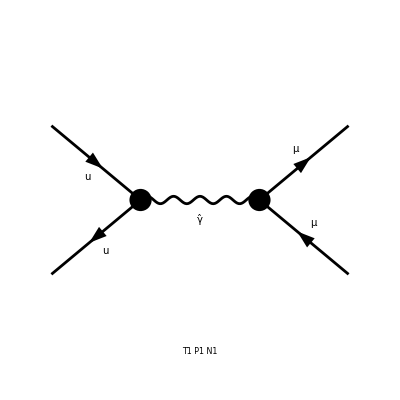

```mathematica
Paint[fieldsBorn];
```

### 1-Loop

```mathematica
fields1L=InsertFields[topologies1L, process];
fields1L=DiagramSelect[fields1L,!FreeQ[#,Field[5]->V[10]]&];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 43 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 43 Particles insertions

#### Paint

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

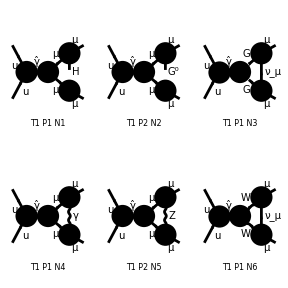

```mathematica
Paint[fields1L];
```

## Diagram Backup

## Save

```mathematica
fieldsBorn>>(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L>>(NotebookDirectory[]<>"backup/fields/fields1L.m");
fields2L>>(NotebookDirectory[]<>"backup/fields/fields2L.m");
```

## Load

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"backup/fields/fields1L.m");
fields2L=<<(NotebookDirectory[]<>"backup/fields/fields2L.m");
```

## Diagram Selection

We want to replicate the selection given by the QEDOnly option of FeynArts. We implement this with the use of DIagramSelect.

```mathematica
(* QEDOnly=ExcludeParticles->{F[1],V[2],V[3],S,SV,U[2],U[3],U[4]} *)
(* QEDOnly as defined in SM.mod *)
```

```mathematica
qedCondition=
(FreeQ[#,F[1,n___]]&&
FreeQ[#,V[2]]&&
FreeQ[#,V[3]]&&
FreeQ[#,S[n_]]&&
FreeQ[#,SV[n_]]&&
FreeQ[#,U[2]]&&
FreeQ[#,U[3]]&&
FreeQ[#,U[4]]&&
FreeQ[#,V[20]]&&
FreeQ[#,V[30]])&;
```

## Selection

```mathematica
fieldsBornQED=DiagramSelect[fieldsBorn,qedCondition];
fields1LQED=DiagramSelect[fields1L,qedCondition];
```

```mathematica
fieldsBornQEDnoT=deleteFermionTriangles[fieldsBornQED];
fields1LQEDnoT=deleteFermionTriangles[fields1LQED];
```

### Born

```mathematica
fieldsBornQED=DiagramSelect[fieldsBorn,qedCondition];
```

#### Paint

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

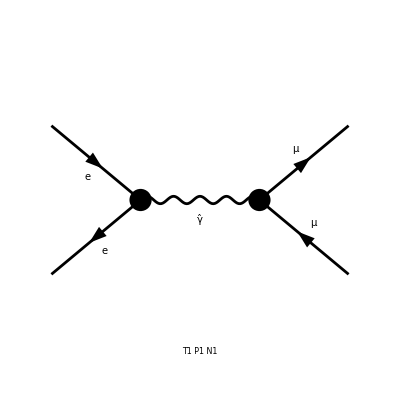

```mathematica
Paint[fieldsBornQEDnoT];
```

### 1-Loop

```mathematica
fields1LQED=DiagramSelect[fields1L,qedCondition];
```

#### Paint

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

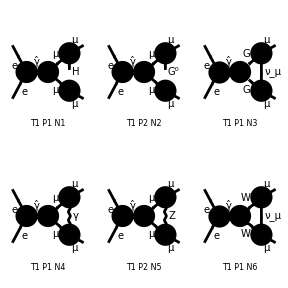

```mathematica
Paint[fields1L];
```

### 2-Loop

```mathematica
fields2LQED=DiagramSelect[fields2L,qedCondition];
```

#### Paint

> Top. 1 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 2 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 3 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 4 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

> Top. 5 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 6 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 7 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

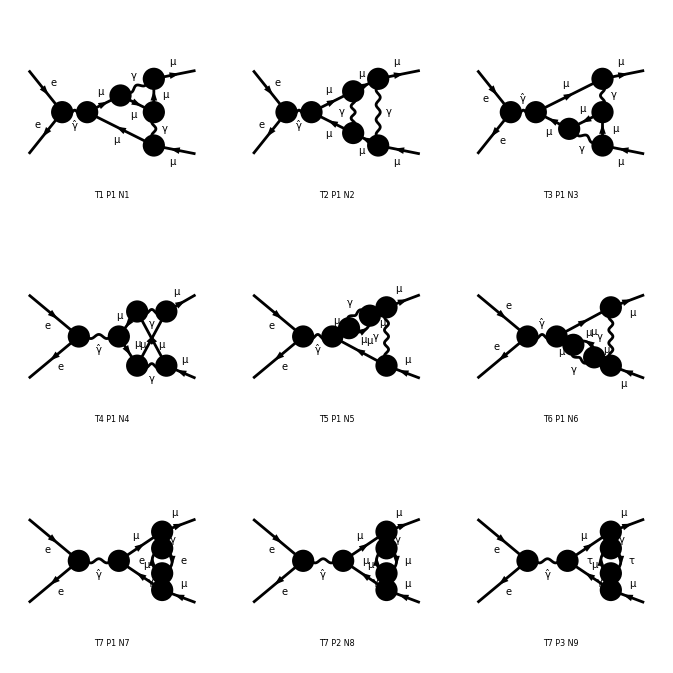

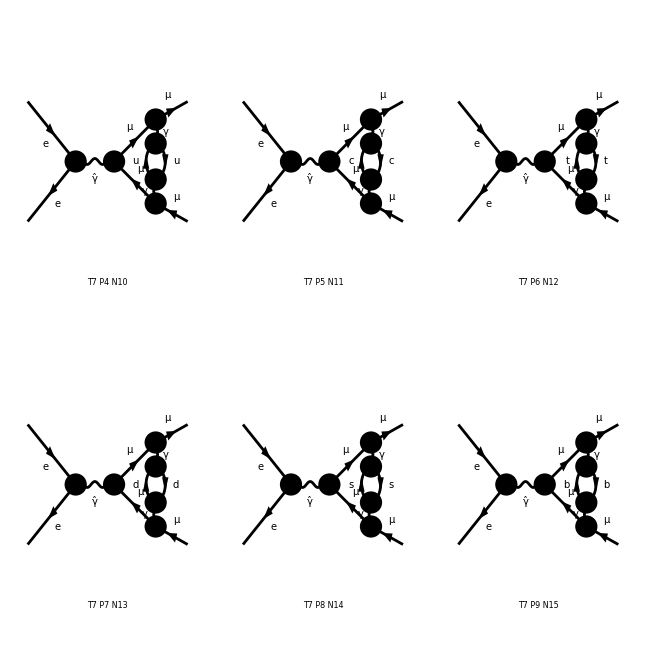

```mathematica
Paint[fields2LQEDnoT];
```

## Interference: 1L - Born

## Amplitudes

### Mass Options

```mathematica
zeroMass={mu->0,md->0};
SetZeroMassParticles[zeroMass]
```

```mathematica
(*myAmpBorn=myAmpBorn/.zeroOnShellMass;
myAmp1L=myAmp1L/.zeroOnShellMass;*)
```

### Computation

```mathematica
ampBorn=CreateFeynAmp[fieldsBornQEDnoT(*,GaugeRules->{}*)];
amp1L=CreateFeynAmp[fields1LQEDnoT(*,GaugeRules->{}*)];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
myAmpBorn=ExtractAmplitude[ampBorn];
myAmp1L=ExtractAmplitude[amp1L];
Print["Born: ", Length[myAmpBorn]]
Print["1L: ", Length[myAmp1L]]
```

Born: 1

1L: 1

```mathematica
SaveAmplitudes[myAmpBorn,OutputName->"BornAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/feynArts_amplitudes/BornAmplitudes.m

```mathematica
SaveAmplitudes[myAmp1L,OutputName->"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/feynArts_amplitudes/OneLoopAmplitudes.m

## Amplitude Backup

```mathematica
myAmpBorn=<<(NotebookDirectory[]<>"feynArts_amplitudes/BornAmplitudes.m");
myAmp1L=<<(NotebookDirectory[]<>"feynArts_amplitudes/OneLoopAmplitudes.m");
Print["Number of diagrams: ", {myAmpBorn,myAmp1L}//Map[Length]]
```

Number of diagrams: {1,1}

Modellistica
analisi
aziende che cercano rpfili qualificati
avere un dottorato vuol dire dimostrare di essere in grado di sviluppare un pensiero scientifico e originale

## Interference

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/equivalence_classes.m

```mathematica
myAmpBorn[[1]]//InputForm
```

FermionChain[NonCommutative[DiracSpinor[-FourMomentum[Incoming, 2], MU]], 
  I*EL*gAu*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[-1]] + 
   I*EL*gAu*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[1]], 
  NonCommutative[DiracSpinor[FourMomentum[Incoming, 1], MU]]]*FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing, 1], MM]], 
  I*EL*gAl*NonCommutative[DiracMatrix[Index[Lorentz, 2]], ChiralityProjector[-1]] + 
   I*EL*gAl*NonCommutative[DiracMatrix[Index[Lorentz, 2]], ChiralityProjector[1]], 
  NonCommutative[DiracSpinor[-FourMomentum[Outgoing, 2], MM]]]*MetricTensor[Index[Lorentz, 1], Index[Lorentz, 2]]*
 PropagatorDenominator[FourMomentum[Outgoing, 1] + FourMomentum[Outgoing, 2], 0]

We need to project the spinor waver function, contrstructing an opportune matrix element which we can contract with the amplitudes for which we need to verify the Ward Identity

```mathematica
proj=I*FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing,1],MM]],1*NonCommutative[ChiralityProjector[-1]]+1*NonCommutative[ChiralityProjector[1]],NonCommutative[DiracSpinor[-FourMomentum[Outgoing,2],MM]]]
```

ⅈ ū[k1,MM].(om_-+om_+).v[k2,MM]

We can verify the results for Born and One Loop case

#### Born

```mathematica
ampBornNoEp=myAmpBorn[[1]]/.removeFermionChain
```

ū[k1,MM].(ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+).v[k2,MM]

```mathematica
AmpSquare[ampBornNoEp*SP[p1+p2,{Lor2}],proj]
```

0

#### 1 Loop

```mathematica
amp1LNoEp=myAmp1L[[1]]/.removeFermionChain
```

ⅈ (2 π)^-d ū[k1,MM].(ⅈ EL gAl ga[Lor3].om_-+ⅈ EL gAl ga[Lor3].om_+).(MM+gs[q1+k1]).(ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+).(MM+gs[q1-k2]).(ⅈ EL gAl ga[Lor4].om_-+ⅈ EL gAl ga[Lor4].om_+).v[k2,MM] FeynAmpDenominator[1/(q1)^2,1/(-MM^2+(q1+k1)^2),1/(-MM^2+(q1-k2)^2)] g[Lor3,Lor4]

```mathematica
AmpSquare[amp1LNoEp*SP[p1+p2,{Lor2}],proj]
```

1/4 PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]] (ⅈ 2^(3-d) EL^3 gAl^3 mm π^-d (4 mm^2-s) SPList[SP[p1,q1]]+ⅈ 2^(3-d) EL^3 gAl^3 mm π^-d (4 mm^2-s) SPList[SP[p2,q1]]+ⅈ 2^(3-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p1,q1]]+ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p2,q1]]-ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p3,q1]]+ⅈ 2^(3-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p2,q1],SP[p2,q1]]-ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p2,q1],SP[p3,q1]])

```mathematica
AmpSquare[amp1LNoEp*SP[p1+p2,{Lor2}],proj]/.s->0
```

1/4 PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]] (ⅈ 2^(5-d) EL^3 gAl^3 mm^3 π^-d SPList[SP[p1,q1]]+ⅈ 2^(5-d) EL^3 gAl^3 mm^3 π^-d SPList[SP[p2,q1]]+ⅈ 2^(3-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p1,q1]]+ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p2,q1]]-ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p3,q1]]+ⅈ 2^(3-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p2,q1],SP[p2,q1]]-ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p2,q1],SP[p3,q1]])

Probably after the kira reduction we will have zero coefficient.

```mathematica
SquareSimplifyAndSave[(myAmp1L/.removeFermionChain)SP[p1+p2,{Lor2}],{proj}]
```

ABISS: Computed contribution 1-1.

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L//interferences/Contribution_1_1.m.

### Substitute

```mathematica
Do[
smi=<<(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_1.m");
smi=smi/.replaceMomenta1;
smi=smi/.replaceMomenta2;
smi>>(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_1.m")
,{i,15}]
```

## Shift

## Squared Matrix Element Backup

```mathematica
sm=Table[<<(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_1.m"),{i,1}]
```

{1/4 PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]] (ⅈ 2^(3-d) EL^3 gAl^3 mm π^-d (4 mm^2-s) SPList[SP[p1,q1]]+ⅈ 2^(3-d) EL^3 gAl^3 mm π^-d (4 mm^2-s) SPList[SP[p2,q1]]+ⅈ 2^(3-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p1,q1]]+ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p2,q1]]-ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p1,q1],SP[p3,q1]]+ⅈ 2^(3-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p2,q1],SP[p2,q1]]-ⅈ 2^(4-d) (-2+d) EL^3 gAl^3 mm π^-d SPList[SP[p2,q1],SP[p3,q1]])}

```mathematica
Variables[sm]
```

{d,EL,gAl,mm,s,PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],SPList[SP[p1,q1]],SPList[SP[p2,q1]],SPList[SP[p1,q1],SP[p1,q1]],SPList[SP[p1,q1],SP[p2,q1]],SPList[SP[p1,q1],SP[p3,q1]],SPList[SP[p2,q1],SP[p2,q1]],SPList[SP[p2,q1],SP[p3,q1]]}

## Shift and Save

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/input/equivalence_classes.m

```mathematica
l=1;
ExtractFamily[sm[[l]]/.ShiftToIntegralFamily[sm[[l]]]]
ShiftToIntegralFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
extractMomenta[sm[[l]]]
```

{A1,{mm}}

{{q1→q1}}

KiraPropagator[q1,0] KiraPropagator[p3+q1,mm] KiraPropagator[-p1-p2+p3+q1,mm]

{q1,p3+q1,-p1-p2+p3+q1}

```mathematica
Do[If[!FreeQ[ShiftToIntegralFamily[sm[[i]]],False],Print[i," ",ShiftToIntegralFamily[sm[[i]]]]],{i,1,1}]
```

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

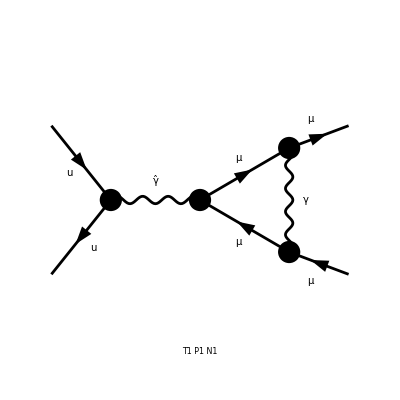

```mathematica
Paint[fields1LQEDnoT];
```

```mathematica
Do[
ShiftAndSave[i,j];
,{i,1,1},{j,1}]
```

ABISS: Integral family {{A1, {mm}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/interferences/Contribution_1_1.m.

## Kira Input

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,1},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/kira_input/Contribution_1_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A1,{mm},0,0,1,0],userIntegral[A1,{mm},0,1,0,0],userIntegral[A1,{mm},1,-1,1,0],userIntegral[A1,{mm},1,0,1,0],userIntegral[A1,{mm},1,1,-1,0],userIntegral[A1,{mm},1,1,0,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Calcolo di r e s

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
Length[si]
```

6

```mathematica
Print["r: ",findR[si]," s: ",findS[si]];
```

r: 2 s: 1

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
GenerateKiraRun[]
```

ABISS: The kira runs have been generated in /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/kira_run/

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A1,{m1},0,0,1,0]→userIntegral[A1,{m1},0,1,0,0],userIntegral[A1,{m1},1,-1,1,0]→(s userIntegral[A1,{m1},0,1,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[A1,{m1},1,1,0,0])/(2 mm^2),userIntegral[A1,{m1},1,0,1,0]→userIntegral[A1,{m1},1,1,0,0],userIntegral[A1,{m1},1,1,-1,0]→(s userIntegral[A1,{m1},0,1,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[A1,{m1},1,1,0,0])/(2 mm^2)}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A1,{mm},0,1,0,0],userIntegral[A1,{mm},1,1,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,1},{j,1}]
```

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/coefficients/Masters.m

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/coefficients/Coefficients_1_1.m

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,1}]
```

### Lagrangian parameter replace

```mathematica
diagramCoefficients
```

{{-ⅈ (-2+d) EL^3 gAl^3 mm (2 π)^-d-ⅈ (-2+d) EL^3 gAl^3 mm (2 π)^(-2 d) (-2^(1+d) π^d+(2 π)^d)+(ⅈ 2^(-2-d) (-2+d) EL^3 gAl^3 π^-d s)/mm-(ⅈ 2^(-2-2 d) (-2+d) EL^3 gAl^3 π^(-2 d) (2^(1+d) π^d-(2 π)^d) s)/mm,0}}

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
coefficients=Plus@@diagramCoefficients //Simplify
```

{0,0}

```mathematica
Length[coefficients]
```

2

```mathematica
Do[
coefficients[[i]]>>(NotebookDirectory[]<>"totalcoeff/Coefficients_"<>ToString[i]<>"_1.m"),
{i,Length[coefficients]}]
```

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m")
```

{userIntegral[A1,{mm},0,1,0,0],userIntegral[A1,{mm},1,1,0,0]}

## Starting Input

## Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
```

## Functions

### Kira Propagator extraction

```mathematica
extractKiraProp[sm_]:=Module[{result,smtmp,kp,p},
smtmp=sm(*//Simplify*);
If[MatchQ[smtmp,PropList[p__]*expr_],
result=smtmp/.PropList[p__]*expr_->{p};
result=Times@@result;
];
If[!MatchQ[smtmp,PropList[p__]*expr_],
result=1;
];
Return[result]
];
```

```mathematica
extractMomenta[sm_]:=Module[{result,kpprod},
kpprod=extractKiraProp[sm];
If[kpprod===1, result={}];
If[Head[kpprod]===KiraPropagator, result=kpprod[[1]]];
If[Head[kpprod]===Times,
result=Map[#[[1]]&,List@@kpprod]
];
Return[result]
];
```

```mathematica
l=2;
ExtractFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

### Analogous integral families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
];
```

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
];
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}];
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/scalar_integrals.m\""}]\).

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/coefficients/Masters.m\""}]\).

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/WardTest/p-mm_1L/kira_myintegrals.m\""}]\).

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

```mathematica
sectorList[si_List]:=Module[{result,l,x},
result=Array[0 &,9];
Do[
l=si[[i]]/.userIntegral[name_,mass_,x__]->{x};
Do[
If[l[[j]]>0,
result[[j]]=1
],
{j,Length[l]}]
,{i,Length[si]}];
Return[result]
]
```

```mathematica
si//sectorList
```

{1,1,1,1,1,1,0,0,0}

```mathematica
si
```

{userIntegral[B3,{mm},-1,1,1,0,1,1,0,0,0],userIntegral[B3,{mm},-1,1,1,1,0,1,0,0,0],userIntegral[B3,{mm},-1,1,1,1,1,1,-1,0,0],userIntegral[B3,{mm},-1,1,1,1,1,1,0,0,-1],userIntegral[B3,{mm},-1,1,1,1,1,1,0,0,0],userIntegral[B3,{mm},0,0,1,0,1,1,0,0,0],userIntegral[B3,{mm},0,0,1,1,0,1,0,0,0],userIntegral[B3,{mm},0,0,1,1,1,1,-1,0,0],userIntegral[B3,{mm},0,0,1,1,1,1,0,0,-1],userIntegral[B3,{mm},0,0,1,1,1,1,0,0,0],userIntegral[B3,{mm},0,1,0,0,1,1,0,0,0],userIntegral[B3,{mm},0,1,0,1,0,1,0,0,0],userIntegral[B3,{mm},0,1,0,1,1,1,-1,0,0],userIntegral[B3,{mm},0,1,0,1,1,1,0,0,-1],userIntegral[B3,{mm},0,1,0,1,1,1,0,0,0],userIntegral[B3,{mm},0,1,1,-1,1,1,0,0,0],userIntegral[B3,{mm},0,1,1,0,0,1,0,0,0],userIntegral[B3,{mm},0,1,1,0,1,0,0,0,0],userIntegral[B3,{mm},0,1,1,0,1,1,-1,0,0],userIntegral[B3,{mm},0,1,1,0,1,1,0,-1,0],userIntegral[B3,{mm},0,1,1,0,1,1,0,0,-1],userIntegral[B3,{mm},0,1,1,0,1,1,0,0,0],userIntegral[B3,{mm},0,1,1,1,-1,1,0,0,0],userIntegral[B3,{mm},0,1,1,1,0,0,0,0,0],userIntegral[B3,{mm},0,1,1,1,0,1,-1,0,0],userIntegral[B3,{mm},0,1,1,1,0,1,0,-1,0],userIntegral[B3,{mm},0,1,1,1,0,1,0,0,-1],userIntegral[B3,{mm},0,1,1,1,0,1,0,0,0],userIntegral[B3,{mm},0,1,1,1,1,0,-1,0,0],userIntegral[B3,{mm},0,1,1,1,1,0,0,0,-1],userIntegral[B3,{mm},0,1,1,1,1,0,0,0,0],userIntegral[B3,{mm},0,1,1,1,1,1,-2,0,0],userIntegral[B3,{mm},0,1,1,1,1,1,-1,-1,0],userIntegral[B3,{mm},0,1,1,1,1,1,-1,0,-1],userIntegral[B3,{mm},0,1,1,1,1,1,-1,0,0],userIntegral[B3,{mm},0,1,1,1,1,1,0,-1,-1],userIntegral[B3,{mm},0,1,1,1,1,1,0,-1,0],userIntegral[B3,{mm},0,1,1,1,1,1,0,0,-1],userIntegral[B3,{mm},0,1,1,1,1,1,0,0,0],userIntegral[B3,{mm},1,-1,1,0,1,1,0,0,0],userIntegral[B3,{mm},1,-1,1,1,0,1,0,0,0],userIntegral[B3,{mm},1,-1,1,1,1,1,-1,0,0],userIntegral[B3,{mm},1,-1,1,1,1,1,0,0,-1],userIntegral[B3,{mm},1,-1,1,1,1,1,0,0,0],userIntegral[B3,{mm},1,0,0,0,1,1,0,0,0],userIntegral[B3,{mm},1,0,0,1,0,1,0,0,0],userIntegral[B3,{mm},1,0,0,1,1,1,-1,0,0],userIntegral[B3,{mm},1,0,0,1,1,1,0,0,-1],userIntegral[B3,{mm},1,0,0,1,1,1,0,0,0],userIntegral[B3,{mm},1,0,1,-1,1,1,0,0,0],userIntegral[B3,{mm},1,0,1,0,0,1,0,0,0],userIntegral[B3,{mm},1,0,1,0,1,0,0,0,0],userIntegral[B3,{mm},1,0,1,0,1,1,-1,0,0],userIntegral[B3,{mm},1,0,1,0,1,1,0,-1,0],userIntegral[B3,{mm},1,0,1,0,1,1,0,0,-1],userIntegral[B3,{mm},1,0,1,0,1,1,0,0,0],userIntegral[B3,{mm},1,0,1,1,-1,1,0,0,0],userIntegral[B3,{mm},1,0,1,1,0,0,0,0,0],userIntegral[B3,{mm},1,0,1,1,0,1,-1,0,0],userIntegral[B3,{mm},1,0,1,1,0,1,0,-1,0],userIntegral[B3,{mm},1,0,1,1,0,1,0,0,-1],userIntegral[B3,{mm},1,0,1,1,0,1,0,0,0],userIntegral[B3,{mm},1,0,1,1,1,0,-1,0,0],userIntegral[B3,{mm},1,0,1,1,1,0,0,0,-1],userIntegral[B3,{mm},1,0,1,1,1,0,0,0,0],userIntegral[B3,{mm},1,0,1,1,1,1,-2,0,0],userIntegral[B3,{mm},1,0,1,1,1,1,-1,-1,0],userIntegral[B3,{mm},1,0,1,1,1,1,-1,0,-1],userIntegral[B3,{mm},1,0,1,1,1,1,-1,0,0],userIntegral[B3,{mm},1,0,1,1,1,1,0,-1,-1],userIntegral[B3,{mm},1,0,1,1,1,1,0,-1,0],userIntegral[B3,{mm},1,0,1,1,1,1,0,0,-2],userIntegral[B3,{mm},1,0,1,1,1,1,0,0,-1],userIntegral[B3,{mm},1,0,1,1,1,1,0,0,0],userIntegral[B3,{mm},1,1,-1,0,1,1,0,0,0],userIntegral[B3,{mm},1,1,-1,1,1,1,-1,0,0],userIntegral[B3,{mm},1,1,-1,1,1,1,0,0,-1],userIntegral[B3,{mm},1,1,-1,1,1,1,0,0,0],userIntegral[B3,{mm},1,1,0,-1,1,1,0,0,0],userIntegral[B3,{mm},1,1,0,0,0,1,0,0,0],userIntegral[B3,{mm},1,1,0,0,1,0,0,0,0],userIntegral[B3,{mm},1,1,0,0,1,1,-1,0,0],userIntegral[B3,{mm},1,1,0,0,1,1,0,-1,0],userIntegral[B3,{mm},1,1,0,0,1,1,0,0,-1],userIntegral[B3,{mm},1,1,0,0,1,1,0,0,0],userIntegral[B3,{mm},1,1,0,1,0,0,0,0,0],userIntegral[B3,{mm},1,1,0,1,0,1,-1,0,0],userIntegral[B3,{mm},1,1,0,1,0,1,0,-1,0],userIntegral[B3,{mm},1,1,0,1,0,1,0,0,-1],userIntegral[B3,{mm},1,1,0,1,0,1,0,0,0],userIntegral[B3,{mm},1,1,0,1,1,0,-1,0,0],userIntegral[B3,{mm},1,1,0,1,1,0,0,0,-1],userIntegral[B3,{mm},1,1,0,1,1,0,0,0,0],userIntegral[B3,{mm},1,1,0,1,1,1,-2,0,0],userIntegral[B3,{mm},1,1,0,1,1,1,-1,-1,0],userIntegral[B3,{mm},1,1,0,1,1,1,-1,0,-1],userIntegral[B3,{mm},1,1,0,1,1,1,-1,0,0],userIntegral[B3,{mm},1,1,0,1,1,1,0,-1,-1],userIntegral[B3,{mm},1,1,0,1,1,1,0,-1,0],userIntegral[B3,{mm},1,1,0,1,1,1,0,0,-2],userIntegral[B3,{mm},1,1,0,1,1,1,0,0,-1],userIntegral[B3,{mm},1,1,0,1,1,1,0,0,0],userIntegral[B3,{mm},1,1,1,-1,1,1,0,-1,0],userIntegral[B3,{mm},1,1,1,-1,1,1,0,0,0],userIntegral[B3,{mm},1,1,1,0,0,1,0,-1,0],userIntegral[B3,{mm},1,1,1,0,0,1,0,0,0],userIntegral[B3,{mm},1,1,1,0,1,0,0,-1,0],userIntegral[B3,{mm},1,1,1,0,1,0,0,0,0],userIntegral[B3,{mm},1,1,1,0,1,1,-1,-1,0],userIntegral[B3,{mm},1,1,1,0,1,1,-1,0,0],userIntegral[B3,{mm},1,1,1,0,1,1,0,-2,0],userIntegral[B3,{mm},1,1,1,0,1,1,0,-1,-1],userIntegral[B3,{mm},1,1,1,0,1,1,0,-1,0],userIntegral[B3,{mm},1,1,1,0,1,1,0,0,-1],userIntegral[B3,{mm},1,1,1,0,1,1,0,0,0],userIntegral[B3,{mm},1,1,1,1,-1,1,0,-1,0],userIntegral[B3,{mm},1,1,1,1,-1,1,0,0,0],userIntegral[B3,{mm},1,1,1,1,0,0,0,-1,0],userIntegral[B3,{mm},1,1,1,1,0,0,0,0,0],userIntegral[B3,{mm},1,1,1,1,0,1,-1,-1,0],userIntegral[B3,{mm},1,1,1,1,0,1,-1,0,0],userIntegral[B3,{mm},1,1,1,1,0,1,0,-2,0],userIntegral[B3,{mm},1,1,1,1,0,1,0,-1,-1],userIntegral[B3,{mm},1,1,1,1,0,1,0,-1,0],userIntegral[B3,{mm},1,1,1,1,0,1,0,0,-1],userIntegral[B3,{mm},1,1,1,1,0,1,0,0,0],userIntegral[B3,{mm},1,1,1,1,1,-1,0,0,0],userIntegral[B3,{mm},1,1,1,1,1,0,-1,-1,0],userIntegral[B3,{mm},1,1,1,1,1,0,-1,0,0],userIntegral[B3,{mm},1,1,1,1,1,0,0,-1,0],userIntegral[B3,{mm},1,1,1,1,1,0,0,0,-1],userIntegral[B3,{mm},1,1,1,1,1,0,0,0,0],userIntegral[B3,{mm},1,1,1,1,1,1,-2,0,0],userIntegral[B3,{mm},1,1,1,1,1,1,-1,-1,-1],userIntegral[B3,{mm},1,1,1,1,1,1,-1,-1,0],userIntegral[B3,{mm},1,1,1,1,1,1,-1,0,-1],userIntegral[B3,{mm},1,1,1,1,1,1,-1,0,0],userIntegral[B3,{mm},1,1,1,1,1,1,0,-2,-1],userIntegral[B3,{mm},1,1,1,1,1,1,0,-2,0],userIntegral[B3,{mm},1,1,1,1,1,1,0,-1,-1],userIntegral[B3,{mm},1,1,1,1,1,1,0,-1,0],userIntegral[B3,{mm},1,1,1,1,1,1,0,0,-2],userIntegral[B3,{mm},1,1,1,1,1,1,0,0,-1],userIntegral[B3,{mm},1,1,1,1,1,1,0,0,0]}

```mathematica
??Export
```

### Find r and s of UserIntegral lists

```mathematica
findR[si_List]:=Module[{rList,result},
rList=Map[sumPlus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
findS[si_List]:=Module[{rList,result},
rList=Map[sumMinus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
sumPlus[ui_userIntegral]:=Module[{indexList,result},
indexList=extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
sumMinus[ui_userIntegral]:=Module[{indexList,result},
indexList=-extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
positive[i_Integer]:=Module[{result},
If[i≥0,result=i];
If[i<0,result=0];
Return[result]
];
```

### Field Insertions manipulations

```mathematica
countInsertions[ins_]:=Module[{result,index},
result=0;
Do[
Do[
result+=Length[ins[[i,2,j,2]]];
,{j,Length[ins[[i,2]]]}];
,{i,Length[ins]}];
Return[result]
]
```

```mathematica
extractTopology[ins_Rule]:=ins[[1]];

extractLoopFields[top_]:=Module[{result},
result=Cases[top,Propagator[Loop[_]][Vertex[a1_][n1_],Vertex[a2_][n2_],f_]:>Rule[{n1,n2},f],Infinity]
]

extractLoopVertices[lines_]:=Module[{result},
result=Cases[lines,Rule[{n1_,n2_},f_]:>{n1,n2},Infinity]
]

next[{a_,b_},c_]:=Module[{result},
If[a=!=c && b=!=c,
result=c,
If[a===c,
result=b,
result=a
]
];
Return[result]
]

sortLoopFields[lines_List]:=Module[{result},
result=SortBy[lines,#[[2,1]]&]
]

triangles[top_]:=Module[{result,lines,vertices,a,b,c,verticesTmp,f1,f2,f3},
result={};
lines=extractLoopFields[top];
vertices=Map[Sort,extractLoopVertices[lines]];
Do[
a=vertices[[i,1]];
b=vertices[[i,2]];
verticesTmp=Delete[vertices,i];
Do[
If[!FreeQ[verticesTmp[[j]],a],
c=next[verticesTmp[[j]],a];
If[(!FreeQ[verticesTmp,Sort[{b,c}]]),
f1=Sort[{a,b}]/.lines;
f2=Sort[{a,c}]/.lines;
f3=Sort[{b,c}]/.lines;
result=AppendTo[result,sortLoopFields[{{Sort[{a,b}],f1},{Sort[{a,c}],f2},{Sort[{b,c}],f3}}]]
]
]
,{j,Length[verticesTmp]}]
,{i,Length[vertices]}];
Return[DeleteDuplicates[result]]
]

fermion[field_]:=Module[{result},
result=field;
If[MatchQ[field,-F[__]],
result=-field
];
Return[result]
]

deleteFermionTriangles[insertion_]:=Module[{result,n,diag,tri,rules,fields,check,deletelist},
n=countInsertions[insertion];
deletelist={};
Do[
diag=DiagramExtract[insertion,i];
tri=triangles[diag[[1,1]]];
rules=List@@diag[[1,2,1,2,1]];
If[tri=!={},
Do[
fields=DeleteDuplicates[Map[fermion[#[[2]]]&,tri[[j]]/.rules]];
If[MatchQ[fields,{F[__]}]||MatchQ[fields,{-F[__]}],
deletelist=AppendTo[deletelist,i]
]
,{j,Length[tri]}]
]
,{i,n}];
deletelist=DeleteDuplicates[deletelist];
result=DiagramDelete[insertion,deletelist];
Return[result]
]
```

### Coefficient Manipulation

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
```

### Remove polarizartion vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[10],p_,i_]->1,Conjugate[PolarizationVector][V[10],p_,i_]->1};
```

```mathematica
removeFermionChain={FermionChain[NonCommutative[DiracSpinor[Times[-1,FourMomentum[Incoming,2]],MU]],Plus[Times[Complex[0,1],EL,gAu,NonCommutative[DiracMatrix[Index[Lorentz,1]],ChiralityProjector[-1]]],Times[Complex[0,1],EL,gAu,NonCommutative[DiracMatrix[Index[Lorentz,1]],ChiralityProjector[1]]]],NonCommutative[DiracSpinor[FourMomentum[Incoming,1],MU]]]->1,MetricTensor[Index[Lorentz,1],Index[Lorentz,2]]->1,PropagatorDenominator[FourMomentum[Outgoing,1]+FourMomentum[Outgoing,2],0]->1};
```

## f

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 2 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 3 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 4 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

> Top. 5 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 6 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 7 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

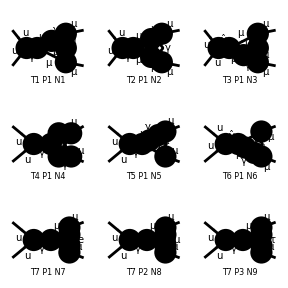

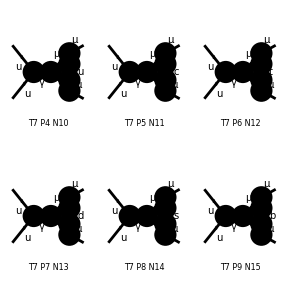

FeynArtsGraphics[{u,u}→{\mu,\mu}][([T1 P1 N1] | [T2 P1 N2] | [T3 P1 N3]
[T4 P1 N4] | [T5 P1 N5] | [T6 P1 N6]
[T7 P1 N7] | [T7 P2 N8] | [T7 P3 N9]),([T7 P4 N10] | [T7 P5 N11] | [T7 P6 N12]
[T7 P7 N13] | [T7 P8 N14] | [T7 P9 N15]
Null | Null | Null)]

```mathematica
Paint[fields2LQEDnoT]
```

```mathematica
li={280000,56000,no,no,3800,4900,no,11000,280000,no,crit,crit,crit,270000,270000}
```

{280000,56000,no,no,3800,4900,no,11000,280000,no,crit,crit,crit,270000,270000}

```mathematica
Do[Print[i, "  ", li[[i]]],{i,Length[li]}]
```

1  280000

2  56000

3  no

4  no

5  3800

6  4900

7  no

8  11000

9  280000

10  no

11  crit

12  crit

13  crit

14  270000

15  270000